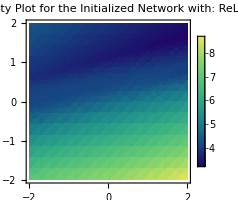
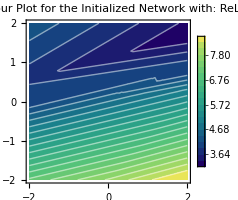
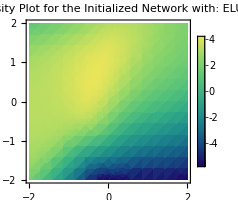
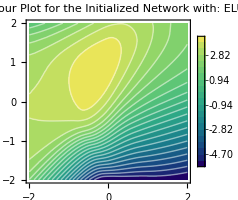
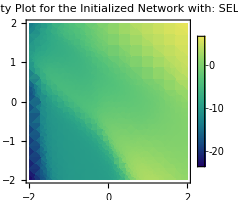
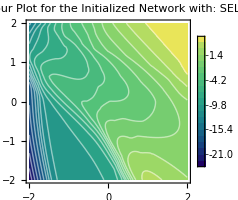
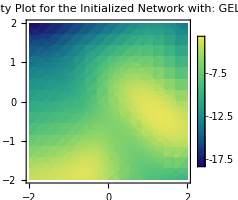
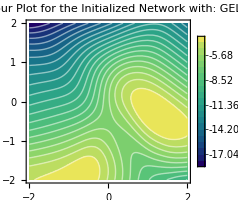

```mathematica
(* The goal of the code is to evaluate and compare various activation functions by incorporating each into a simple neural network, initializing the network randomly,and then visualizing the resulting output landscapes. This is achieved by generating density and contour plots for the network's output over a 2D grid,allowing the examination of the smoothness and structure of the output landscapes. These visualizations facilitate the comparison of how different activation functions affect the network's behavior, providing insights into their impact on the network's smoothness and optimization efficiency: *)

(* Set up an array for activation functions to be tested: *)
activationFunctionsList={
"ReLU","ELU","SELU","GELU",
"Swish","HardSwish","Mish","SoftPlus",
"HardTanh","HardSigmoid","Sigmoid",Tanh
};

(* Loop through each activation function, train a neural network, and record the results: *)
activationFunctionResults=Table[
Module[
{neuralNetwork,initializedNetwork},
(* Define a simple neural network structure: *)
neuralNetwork=NetChain[
{
(* First hidden layer with the specified activation function: *)
LinearLayer[5],ElementwiseLayer[activationFunction],
(* Second hidden layer with the specified activation function: *)
LinearLayer[5],ElementwiseLayer[activationFunction],
(* Third hidden layer with the specified activation function: *)
LinearLayer[5],ElementwiseLayer[activationFunction],
(* Output layer with linear activation function: *)
LinearLayer[1]
},
"Input"->2
];
(* Initialize the network with random weights and biases: *)
initializedNetwork=NetInitialize[
neuralNetwork,
(* Initialization method with specified weights and biases: *)
Method->{"Random","Weights"->1,"Biases"->1},
RandomSeeding->Automatic
];
{
(* Generate a density plot for the initialized network's output over a 2D grid: *)
DensityPlot[
(* Evaluate the initialized network on the 2D grid defined by x and y: *)
initializedNetwork[{x,y}],
{x,-2,2},
{y,-2,2},
PlotLabel->Style[Row[{"Density Plot for the Initialized\nNetwork with: ",activationFunction}],13,Bold],
PlotLegends->Automatic,
ImageSize->200,
ColorFunction->"BlueGreenYellow"
],
(* Generate a contour plot for the initialized network's output over a 2D grid: *)
ContourPlot[
(* Evaluate the initialized network on the 2D grid defined by x and y: *)
initializedNetwork[{x,y}],
{x,-2,2},
{y,-2,2},
PlotLabel->Style[Row[{"Contour Plot for the Initialized\nNetwork with: ",activationFunction}],13,Bold],
PlotLegends->Automatic,
ImageSize->200,
Contours->20,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow"
]
}
],
(* Iterate over the array of activation functions: *)
{activationFunction,activationFunctionsList}
]
```